## 1. Постановка задачі

Задача Діріхле для еліптичного рівняння на двовимірній області 

	L[u] = -μΔu + β∇u +σu = f		Ω=[0,1]x[0,1]			(1)
				u|_Γ = 0						(2)
				
Ми розглядаємо задачу зі сталими коефіцієнтами, тому 

	u=(x,y),	f=f(x,y),	μ=const,   β=const,   σ=const.		(3)

```mathematica
(* Блок ініціалізації вхідних параметрів *)
μ=Function[{x,y},100];
β=Function[{x,y},1];
σ=Function[{x,y},1];
f=Function[{x,y},100000];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$pathToFile="square.node";
stmp = OpenWrite[$pathToFile];

WriteString[stmp,"5 2 0 0 \n"];

(* == <vertex #> <x> <y> [attributes] [boundary marker] *)
WriteString[stmp, "1 0.0 0.0 \n"];
WriteString[stmp, "2 1.0 0.0 \n"];
WriteString[stmp, "3 1.0 1.0 \n"];
WriteString[stmp, "4 0.5 0.5 \n"];
WriteString[stmp, "5 0.0 1.0"];
Close[stmp];
```

### Execution of triangulation program

```mathematica
$triangleCmd= "./triangle -u ";
commandToRun =$triangleCmd<>"square.node";
(*commandToRun = $triangleCmd<>"A.poly";*)
Run[commandToRun];
```

### Data input

```mathematica
triangles=Import["square.1.ele","Table"];
(*triangles=Import["A.1.ele","Table"];*)
(*Results in list of vetrices forming triangles*)
triangles=Delete[triangles,-1];
triangles=Delete[triangles,1];
For[i=1,i<=Length[triangles],i++,
triangles[[i]]=Delete[triangles[[i]],1]
];
Print["Triangles are: ",triangles];


nodes=Import["square.1.node","Table"];
(*nodes=Import["A.1.node", "Table"];*)
(*Results in list of vetrices*)
nodes=Delete[nodes,-1];
nodes=Delete[nodes,1];
For[i=1,i<=Length[nodes],i++,
nodes[[i]]=Delete[nodes[[i]],1];
];

Print["Nodes are: ", nodes];
```

Triangles are: {{14,8,22},{10,11,12},{18,10,12},{39,12,20},{23,10,14},{50,4,36},{18,7,17},{15,7,9},{29,30,8},{38,33,1},{7,29,17},{19,12,39},{51,35,28},{12,11,20},{67,53,70},{27,24,28},{51,32,35},{4,48,61},{14,17,8},{19,13,25},{12,19,18},{9,28,35},{42,45,65},{66,47,42},{27,26,25},{17,10,18},{15,37,36},{7,18,21},{38,13,19},{17,29,8},{19,25,21},{21,18,19},{69,32,34},{7,21,9},{61,48,41},{60,70,53},{11,10,23},{10,17,14},{14,6,23},{13,27,25},{9,26,28},{27,28,26},{25,26,21},{36,4,15},{26,9,21},{7,15,29},{29,15,30},{4,30,15},{45,42,47},{56,64,69},{15,9,37},{35,32,37},{9,35,37},{38,19,39},{54,36,37},{51,28,24},{68,70,71},{57,2,63},{24,49,51},{34,31,57},{48,55,53},{33,38,39},{39,20,33},{20,1,33},{52,6,22},{41,16,61},{58,62,60},{6,14,22},{67,43,66},{52,22,59},{48,53,67},{16,30,61},{59,22,44},{46,59,45},{44,65,59},{44,16,65},{67,66,41},{16,44,8},{50,48,4},{65,45,59},{61,30,4},{5,45,47},{58,64,40},{55,58,60},{60,53,55},{31,51,49},{8,30,16},{52,59,46},{65,16,41},{54,50,36},{57,63,34},{44,22,8},{51,31,34},{55,50,54},{62,58,40},{32,54,37},{45,5,46},{69,63,56},{32,51,34},{64,55,54},{55,64,58},{55,48,50},{47,66,43},{41,42,65},{2,56,63},{69,64,54},{40,64,56},{66,42,41},{48,67,41},{60,71,70},{71,3,68},{70,43,67},{32,69,54},{69,34,63},{43,70,68},{60,62,71},{3,71,62}}

Nodes are: {{0,0,1},{1,0,1},{1,1,1},{0.5,0.5,0},{0,1,1},{0,0.5,1},{0.328964,0.270834,0},{0.25,0.5,0},{0.447493,0.234496,0},{0.109375,0.3125,0},{0,0.25,1},{0.0938616,0.212695,0},{0.25,0,1},{0.125,0.4375,0},{0.426238,0.376643,0},{0.333616,0.616137,0},{0.242188,0.359375,0},{0.207473,0.246144,0},{0.184241,0.115384,0},{0,0.125,1},{0.287317,0.164514,0},{0.139323,0.565104,0},{0,0.375,1},{0.5,0,1},{0.262625,0.0836257,0},{0.357821,0.0987788,0},{0.375,0,1},{0.454213,0.0993788,0},{0.334663,0.363213,0},{0.364824,0.476475,0},{0.75,0,1},{0.637136,0.219685,0},{0.0431028,0.0625,0},{0.766959,0.147548,0},{0.526908,0.17072,0},{0.545547,0.389033,0},{0.540663,0.269181,0},{0.125,0,1},{0.0921346,0.120465,0},{1,0.5,1},{0.362338,0.756331,0},{0.27434,0.863492,0},{0.5,1,1},{0.234108,0.599611,0},{0.124928,0.841679,0},{0,0.75,1},{0.25,1,1},{0.520649,0.609935,0},{0.625,0,1},{0.614489,0.482162,0},{0.622703,0.112221,0},{0,0.625,1},{0.588959,0.698511,0},{0.666431,0.324081,0},{0.721681,0.526159,0},{1,0.25,1},{0.875,0,1},{0.865578,0.563481,0},{0.109405,0.6875,0},{0.756008,0.689872,0},{0.419571,0.562027,0},{1,0.75,1},{0.9375,0.125,0},{0.834645,0.386682,0},{0.233396,0.731013,0},{0.413567,0.88811,0},{0.48974,0.782651,0},{0.75,1,1},{0.781336,0.272625,0},{0.643345,0.863215,0},{0.8065,0.845972,0}}

### Visualization

{{{0.125,0.4375},{0.25,0.5},{0.139323,0.565104},{0.125,0.4375}},{{0.109375,0.3125},{0,0.25},{0.0938616,0.212695},{0.109375,0.3125}},{{0.207473,0.246144},{0.109375,0.3125},{0.0938616,0.212695},{0.207473,0.246144}},{{0.0921346,0.120465},{0.0938616,0.212695},{0,0.125},{0.0921346,0.120465}},{{0,0.375},{0.109375,0.3125},{0.125,0.4375},{0,0.375}},{{0.614489,0.482162},{0.5,0.5},{0.545547,0.389033},{0.614489,0.482162}},{{0.207473,0.246144},{0.328964,0.270834},{0.242188,0.359375},{0.207473,0.246144}},{{0.426238,0.376643},{0.328964,0.270834},{0.447493,0.234496},{0.426238,0.376643}},{{0.334663,0.363213},{0.364824,0.476475},{0.25,0.5},{0.334663,0.363213}},{{0.125,0},{0.0431028,0.0625},{0,0},{0.125,0}},{{0.328964,0.270834},{0.334663,0.363213},{0.242188,0.359375},{0.328964,0.270834}},{{0.184241,0.115384},{0.0938616,0.212695},{0.0921346,0.120465},{0.184241,0.115384}},{{0.622703,0.112221},{0.526908,0.17072},{0.454213,0.0993788},{0.622703,0.112221}},{{0.0938616,0.212695},{0,0.25},{0,0.125},{0.0938616,0.212695}},{{0.48974,0.782651},{0.588959,0.698511},{0.643345,0.863215},{0.48974,0.782651}},{{0.375,0},{0.5,0},{0.454213,0.0993788},{0.375,0}},{{0.622703,0.112221},{0.637136,0.219685},{0.526908,0.17072},{0.622703,0.112221}},{{0.5,0.5},{0.520649,0.609935},{0.419571,0.562027},{0.5,0.5}},{{0.125,0.4375},{0.242188,0.359375},{0.25,0.5},{0.125,0.4375}},{{0.184241,0.115384},{0.25,0},{0.262625,0.0836257},{0.184241,0.115384}},{{0.0938616,0.212695},{0.184241,0.115384},{0.207473,0.246144},{0.0938616,0.212695}},{{0.447493,0.234496},{0.454213,0.0993788},{0.526908,0.17072},{0.447493,0.234496}},{{0.27434,0.863492},{0.124928,0.841679},{0.233396,0.731013},{0.27434,0.863492}},{{0.413567,0.88811},{0.25,1},{0.27434,0.863492},{0.413567,0.88811}},{{0.375,0},{0.357821,0.0987788},{0.262625,0.0836257},{0.375,0}},{{0.242188,0.359375},{0.109375,0.3125},{0.207473,0.246144},{0.242188,0.359375}},{{0.426238,0.376643},{0.540663,0.269181},{0.545547,0.389033},{0.426238,0.376643}},{{0.328964,0.270834},{0.207473,0.246144},{0.287317,0.164514},{0.328964,0.270834}},{{0.125,0},{0.25,0},{0.184241,0.115384},{0.125,0}},{{0.242188,0.359375},{0.334663,0.363213},{0.25,0.5},{0.242188,0.359375}},{{0.184241,0.115384},{0.262625,0.0836257},{0.287317,0.164514},{0.184241,0.115384}},{{0.287317,0.164514},{0.207473,0.246144},{0.184241,0.115384},{0.287317,0.164514}},{{0.781336,0.272625},{0.637136,0.219685},{0.766959,0.147548},{0.781336,0.272625}},{{0.328964,0.270834},{0.287317,0.164514},{0.447493,0.234496},{0.328964,0.270834}},{{0.419571,0.562027},{0.520649,0.609935},{0.362338,0.756331},{0.419571,0.562027}},{{0.756008,0.689872},{0.643345,0.863215},{0.588959,0.698511},{0.756008,0.689872}},{{0,0.25},{0.109375,0.3125},{0,0.375},{0,0.25}},{{0.109375,0.3125},{0.242188,0.359375},{0.125,0.4375},{0.109375,0.3125}},{{0.125,0.4375},{0,0.5},{0,0.375},{0.125,0.4375}},{{0.25,0},{0.375,0},{0.262625,0.0836257},{0.25,0}},{{0.447493,0.234496},{0.357821,0.0987788},{0.454213,0.0993788},{0.447493,0.234496}},{{0.375,0},{0.454213,0.0993788},{0.357821,0.0987788},{0.375,0}},{{0.262625,0.0836257},{0.357821,0.0987788},{0.287317,0.164514},{0.262625,0.0836257}},{{0.545547,0.389033},{0.5,0.5},{0.426238,0.376643},{0.545547,0.389033}},{{0.357821,0.0987788},{0.447493,0.234496},{0.287317,0.164514},{0.357821,0.0987788}},{{0.328964,0.270834},{0.426238,0.376643},{0.334663,0.363213},{0.328964,0.270834}},{{0.334663,0.363213},{0.426238,0.376643},{0.364824,0.476475},{0.334663,0.363213}},{{0.5,0.5},{0.364824,0.476475},{0.426238,0.376643},{0.5,0.5}},{{0.124928,0.841679},{0.27434,0.863492},{0.25,1},{0.124928,0.841679}},{{1,0.25},{0.834645,0.386682},{0.781336,0.272625},{1,0.25}},{{0.426238,0.376643},{0.447493,0.234496},{0.540663,0.269181},{0.426238,0.376643}},{{0.526908,0.17072},{0.637136,0.219685},{0.540663,0.269181},{0.526908,0.17072}},{{0.447493,0.234496},{0.526908,0.17072},{0.540663,0.269181},{0.447493,0.234496}},{{0.125,0},{0.184241,0.115384},{0.0921346,0.120465},{0.125,0}},{{0.666431,0.324081},{0.545547,0.389033},{0.540663,0.269181},{0.666431,0.324081}},{{0.622703,0.112221},{0.454213,0.0993788},{0.5,0},{0.622703,0.112221}},{{0.75,1},{0.643345,0.863215},{0.8065,0.845972},{0.75,1}},{{0.875,0},{1,0},{0.9375,0.125},{0.875,0}},{{0.5,0},{0.625,0},{0.622703,0.112221},{0.5,0}},{{0.766959,0.147548},{0.75,0},{0.875,0},{0.766959,0.147548}},{{0.520649,0.609935},{0.721681,0.526159},{0.588959,0.698511},{0.520649,0.609935}},{{0.0431028,0.0625},{0.125,0},{0.0921346,0.120465},{0.0431028,0.0625}},{{0.0921346,0.120465},{0,0.125},{0.0431028,0.0625},{0.0921346,0.120465}},{{0,0.125},{0,0},{0.0431028,0.0625},{0,0.125}},{{0,0.625},{0,0.5},{0.139323,0.565104},{0,0.625}},{{0.362338,0.756331},{0.333616,0.616137},{0.419571,0.562027},{0.362338,0.756331}},{{0.865578,0.563481},{1,0.75},{0.756008,0.689872},{0.865578,0.563481}},{{0,0.5},{0.125,0.4375},{0.139323,0.565104},{0,0.5}},{{0.48974,0.782651},{0.5,1},{0.413567,0.88811},{0.48974,0.782651}},{{0,0.625},{0.139323,0.565104},{0.109405,0.6875},{0,0.625}},{{0.520649,0.609935},{0.588959,0.698511},{0.48974,0.782651},{0.520649,0.609935}},{{0.333616,0.616137},{0.364824,0.476475},{0.419571,0.562027},{0.333616,0.616137}},{{0.109405,0.6875},{0.139323,0.565104},{0.234108,0.599611},{0.109405,0.6875}},{{0,0.75},{0.109405,0.6875},{0.124928,0.841679},{0,0.75}},{{0.234108,0.599611},{0.233396,0.731013},{0.109405,0.6875},{0.234108,0.599611}},{{0.234108,0.599611},{0.333616,0.616137},{0.233396,0.731013},{0.234108,0.599611}},{{0.48974,0.782651},{0.413567,0.88811},{0.362338,0.756331},{0.48974,0.782651}},{{0.333616,0.616137},{0.234108,0.599611},{0.25,0.5},{0.333616,0.616137}},{{0.614489,0.482162},{0.520649,0.609935},{0.5,0.5},{0.614489,0.482162}},{{0.233396,0.731013},{0.124928,0.841679},{0.109405,0.6875},{0.233396,0.731013}},{{0.419571,0.562027},{0.364824,0.476475},{0.5,0.5},{0.419571,0.562027}},{{0,1},{0.124928,0.841679},{0.25,1},{0,1}},{{0.865578,0.563481},{0.834645,0.386682},{1,0.5},{0.865578,0.563481}},{{0.721681,0.526159},{0.865578,0.563481},{0.756008,0.689872},{0.721681,0.526159}},{{0.756008,0.689872},{0.588959,0.698511},{0.721681,0.526159},{0.756008,0.689872}},{{0.75,0},{0.622703,0.112221},{0.625,0},{0.75,0}},{{0.25,0.5},{0.364824,0.476475},{0.333616,0.616137},{0.25,0.5}},{{0,0.625},{0.109405,0.6875},{0,0.75},{0,0.625}},{{0.233396,0.731013},{0.333616,0.616137},{0.362338,0.756331},{0.233396,0.731013}},{{0.666431,0.324081},{0.614489,0.482162},{0.545547,0.389033},{0.666431,0.324081}},{{0.875,0},{0.9375,0.125},{0.766959,0.147548},{0.875,0}},{{0.234108,0.599611},{0.139323,0.565104},{0.25,0.5},{0.234108,0.599611}},{{0.622703,0.112221},{0.75,0},{0.766959,0.147548},{0.622703,0.112221}},{{0.721681,0.526159},{0.614489,0.482162},{0.666431,0.324081},{0.721681,0.526159}},{{1,0.75},{0.865578,0.563481},{1,0.5},{1,0.75}},{{0.637136,0.219685},{0.666431,0.324081},{0.540663,0.269181},{0.637136,0.219685}},{{0.124928,0.841679},{0,1},{0,0.75},{0.124928,0.841679}},{{0.781336,0.272625},{0.9375,0.125},{1,0.25},{0.781336,0.272625}},{{0.637136,0.219685},{0.622703,0.112221},{0.766959,0.147548},{0.637136,0.219685}},{{0.834645,0.386682},{0.721681,0.526159},{0.666431,0.324081},{0.834645,0.386682}},{{0.721681,0.526159},{0.834645,0.386682},{0.865578,0.563481},{0.721681,0.526159}},{{0.721681,0.526159},{0.520649,0.609935},{0.614489,0.482162},{0.721681,0.526159}},{{0.25,1},{0.413567,0.88811},{0.5,1},{0.25,1}},{{0.362338,0.756331},{0.27434,0.863492},{0.233396,0.731013},{0.362338,0.756331}},{{1,0},{1,0.25},{0.9375,0.125},{1,0}},{{0.781336,0.272625},{0.834645,0.386682},{0.666431,0.324081},{0.781336,0.272625}},{{1,0.5},{0.834645,0.386682},{1,0.25},{1,0.5}},{{0.413567,0.88811},{0.27434,0.863492},{0.362338,0.756331},{0.413567,0.88811}},{{0.520649,0.609935},{0.48974,0.782651},{0.362338,0.756331},{0.520649,0.609935}},{{0.756008,0.689872},{0.8065,0.845972},{0.643345,0.863215},{0.756008,0.689872}},{{0.8065,0.845972},{1,1},{0.75,1},{0.8065,0.845972}},{{0.643345,0.863215},{0.5,1},{0.48974,0.782651},{0.643345,0.863215}},{{0.637136,0.219685},{0.781336,0.272625},{0.666431,0.324081},{0.637136,0.219685}},{{0.781336,0.272625},{0.766959,0.147548},{0.9375,0.125},{0.781336,0.272625}},{{0.5,1},{0.643345,0.863215},{0.75,1},{0.5,1}},{{0.756008,0.689872},{1,0.75},{0.8065,0.845972},{0.756008,0.689872}},{{1,1},{0.8065,0.845972},{1,0.75},{1,1}}}

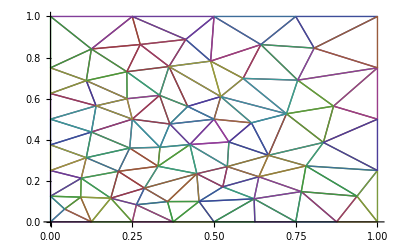

```mathematica
(*make list of edges grouped by triangles [[tris]] 
and ListLinePlot[{tris[[1]],..,tris[[n]]] them.*)

getVertexXY:=Function[{triangleNumber,vertexNumber},
Delete[nodes[[triangles[[triangleNumber,vertexNumber]]]],-1]
];
(*list of triangle vertecies for complete triangle drawing*)
toFormTriangle={1,2,3,1};

(* array of triangles *)
tris={{}};
For[i=1,i<=Length[triangles],i++,
self={{}};
For[j=1,j<=Length[toFormTriangle],j++,
self=Append[self,getVertexXY[i,toFormTriangle[[j]]]];
];
self=Delete[self,1];
tris=Append[tris,self];
]
tris=Delete[tris,1];
Print[tris];

ListLinePlot[tris]
```

```mathematica
Length[tris]
```

117

-----------------------------------------------------FEM Procedure----------------------------------------------------

```mathematica
(* number of the finite elements *) 
nel=Length[triangles];
(* number of nods of triangulation *) 
nod =Length[nodes];
(* nod quantity of finite element *) 
nodTriangl=3;
(* list of equation numbers *)
neq=Table[0,{i,1,nod}];
(* list of boundary point numbers of equations *)
boundpoint = {};
For[i=1, i≤ Length[nodes], i++, If[nodes[[i]][[3]]==1, AppendTo[boundpoint, i]]];
Boundsort=Sort[boundpoint];
Print["BoundSort pooints: ", boundpoint];
(* number of boundary nods *)
numBoundCond=Length[boundpoint];
(* number of boundary nods with Dirichlets BC *)
nodDirichl=numBoundCond;
```

BoundSort pooints: {1,2,3,5,6,11,13,20,23,24,27,31,38,40,43,46,47,49,52,56,57,62,68}

```mathematica
(*   ========   Order of equations   ========    *)
  i=nv=0;m=1;k=0;For[i=1,i≤nod,i++,If[i≠Boundsort⟦m⟧,neq⟦i⟧=nv=nv+1,{neq⟦i⟧=k=k-1,If[m<numBoundCond,m=m+1]}]];
Print["Order of equation: ",nv];
```

Order of equation: 48

```mathematica
Print["neq=",neq,"  nv=",nv,"  k=",k];
(*   ========   Bandwidth of matrix   ========    *)
gband=0;
For[e=1,e≤nel,e++,For[l=1,l<3,l++,n=triangles⟦e,l⟧;equat=neq⟦n⟧;If[equat>0,For[m=l+1,m≤3,m++,k=triangles⟦e,m⟧;colum=neq⟦k⟧;
If[colum>0,i=Abs[equat-colum];If[i>gband,gband=i]];
]]]];
Print["Bandwidth of matrix=",2*gband+1];
```

neq={-1,-2,-3,1,-4,-5,2,3,4,5,-6,6,-7,7,8,9,10,11,12,-8,13,14,-9,-10,15,16,-11,17,18,19,-12,20,21,22,23,24,25,-13,26,-14,27,28,-15,29,30,-16,-17,31,-18,32,33,-19,34,35,36,-20,-21,37,38,39,40,-22,41,42,43,44,45,-23,46,47,48}  nv=48  k=-23

Bandwidth of matrix=79

```mathematica
matrix=Table[0.,{i,1,nv},{j,1,nv}];
vektor=Table[0.,{i,1,nv}];
width=2*gband+1;
matX=Table[0.,{i,1,nv},{j,1,width}];
vekR=Table[0.,{i,1,nv}];
```

```mathematica
(*   ========   Loop of  finite elements   ========  *)
For[e=1,e≤nel,e++,
i=triangles⟦e,1⟧;j=triangles⟦e,2⟧;m=triangles⟦e,3⟧;
bi=nodes⟦j,2⟧-nodes⟦m,2⟧;ci=nodes⟦m,1⟧-nodes⟦j,1⟧;
bj=nodes⟦m,2⟧-nodes⟦i,2⟧;cj=nodes⟦i,1⟧-nodes⟦m,1⟧;
bm=nodes⟦i,2⟧-nodes⟦j,2⟧;cm=nodes⟦j,1⟧-nodes⟦i,1⟧;
dt=bi*cj-bj*ci;
ke=1./dt*({{bi*bi+ci*ci, bi*bj+ci*cj, bi*bm+ci*cm}, {bi*bj+ci*cj, bj*bj+cj*cj, bj*bm+cj*cm}, {bm*bi+cm*ci, bm*bj+cm*cj, bm*bm+cm*cm}});
xs=1/3.*(nodes⟦m,1⟧+nodes⟦j,1⟧+nodes⟦i,1⟧);ys=1/3.*(nodes⟦m,2⟧+nodes⟦j,2⟧+nodes⟦i,2⟧);
me=ω^2*dt/24.*({{2., 1., 1.}, {1., 2., 1.}, {1., 1., 2.}});fe=dt/6.*f[xs,ys]*({{1.}, {1.}, {1.}});
Print["e=",e," dt=",dt,"  determinant K_e=",Det[ke]];
(*   ===    Assembling of FEM equations    =====   *)
For[i=1,i≤nodTriangl,i++,
n=triangles⟦e,i⟧;equat=neq⟦n⟧;
If[equat>0,
For[j=1,j≤nodTriangl,j++,
k=triangles⟦e,j⟧;colomn=neq⟦k⟧;
If[colomn>0,
matrix⟦equat,colomn⟧=matrix⟦equat,colomn⟧+ke⟦i,j⟧]
];
vektor⟦equat⟧=vektor⟦equat⟧+fe⟦i,1⟧]
]; 
(*   ========    Assembling of FEM equations    ========   *)
For[i=1,i≤nodTriangl,i++,
n=triangles⟦e,i⟧;equat=neq⟦n⟧;
If[equat>0,
For[j=1,j≤nodTriangl,j++,
k=triangles⟦e,j⟧;colomn=neq⟦k⟧;
If[colomn>0,pl=colomn-equat+gband+1;
matX⟦equat,pl⟧=matX⟦equat,pl⟧+ke⟦i,j⟧]
];
vekR⟦equat⟧=vekR⟦equat⟧+fe⟦i,1⟧]
]];
Print["  matrix=",MatrixForm[matrix],"  vektor=",MatrixForm[vektor]];    Print["  matrix=",MatrixForm[matX],"  vektor=",MatrixForm[vekR]];
```

e=1 dt=0.0150553  determinant K_e=2.22045×10^-16

e=2 dt=0.00994655  determinant K_e=0.

e=3 dt=0.0108201  determinant K_e=4.44089×10^-16

e=4 dt=0.0085054  determinant K_e=3.33067×10^-16

e=5 dt=0.0146484  determinant K_e=-1.11022×10^-16

e=6 dt=0.011892  determinant K_e=3.33067×10^-16

e=7 dt=0.0128994  determinant K_e=2.22045×10^-16

e=8 dt=0.0160762  determinant K_e=0.

e=9 dt=0.0137148  determinant K_e=0.

e=10 dt=0.0078125  determinant K_e=2.22045×10^-16

e=11 dt=0.00852089  determinant K_e=-1.11022×10^-16

e=12 dt=0.00850371  determinant K_e=2.22045×10^-16

e=13 dt=0.0110867  determinant K_e=9.99201×10^-16

e=14 dt=0.0117327  determinant K_e=-1.11022×10^-16

e=15 dt=0.0209179  determinant K_e=-2.22045×10^-16

e=16 dt=0.0124223  determinant K_e=-4.44089×10^-16

e=17 dt=0.0111388  determinant K_e=-2.22045×10^-16

e=18 dt=0.0101228  determinant K_e=-4.44089×10^-16

e=19 dt=0.0170898  determinant K_e=-4.44089×10^-16

e=20 dt=0.00695585  determinant K_e=-6.66134×10^-16

e=21 dt=0.0140787  determinant K_e=3.33067×10^-16

e=22 dt=0.0103017  determinant K_e=1.11022×10^-16

e=23 dt=0.0189007  determinant K_e=-2.22045×10^-16

e=24 dt=0.0196048  determinant K_e=2.22045×10^-16

e=25 dt=0.00966368  determinant K_e=-2.22045×10^-16

e=26 dt=0.0134113  determinant K_e=2.22045×10^-16

e=27 dt=0.0142389  determinant K_e=-1.11022×10^-16

e=28 dt=0.0118886  determinant K_e=-2.22045×10^-16

e=29 dt=0.014423  determinant K_e=-3.33067×10^-16

e=30 dt=0.0129743  determinant K_e=1.11022×10^-16

e=31 dt=0.00712454  determinant K_e=-4.44089×10^-16

e=32 dt=0.0123368  determinant K_e=6.66134×10^-16

e=33 dt=0.017275  determinant K_e=-2.22045×10^-16

e=34 dt=0.0141154  determinant K_e=-1.11022×10^-16

e=35 dt=0.0223819  determinant K_e=-1.11022×10^-16

e=36 dt=0.0279836  determinant K_e=3.33067×10^-16

e=37 dt=0.0136719  determinant K_e=-4.44089×10^-16

e=38 dt=0.0158691  determinant K_e=-1.11022×10^-16

e=39 dt=0.015625  determinant K_e=0.

e=40 dt=0.0104532  determinant K_e=-4.44089×10^-16

e=41 dt=0.0130283  determinant K_e=-4.44089×10^-16

e=42 dt=0.00953187  determinant K_e=6.66134×10^-16

e=43 dt=0.0073261  determinant K_e=0.

e=44 dt=0.0138038  determinant K_e=-3.33067×10^-16

e=45 dt=0.0154632  determinant K_e=5.55112×10^-16

e=46 dt=0.00838309  determinant K_e=-1.11022×10^-16

e=47 dt=0.00996692  determinant K_e=1.11022×10^-16

e=48 dt=0.0149396  determinant K_e=4.44089×10^-16

e=49 dt=0.0209269  determinant K_e=4.44089×10^-16

e=50 dt=0.0261464  determinant K_e=-6.66134×10^-16

e=51 dt=0.0139812  determinant K_e=-2.22045×10^-16

e=52 dt=0.0101796  determinant K_e=-1.11022×10^-16

e=53 dt=0.00869653  determinant K_e=-1.11022×10^-16

e=54 dt=0.0109286  determinant K_e=0.

e=55 dt=0.0148054  determinant K_e=0.

e=56 dt=0.0173322  determinant K_e=0.

e=57 dt=0.0241561  determinant K_e=-3.33067×10^-16

e=58 dt=0.015625  determinant K_e=-1.11022×10^-16

e=59 dt=0.0140276  determinant K_e=2.22045×10^-16

e=60 dt=0.0184435  determinant K_e=0.

e=61 dt=0.0235294  determinant K_e=-6.10623×10^-16

e=62 dt=0.00781169  determinant K_e=0.

e=63 dt=0.00556296  determinant K_e=4.44089×10^-16

e=64 dt=0.00538785  determinant K_e=3.33067×10^-16

e=65 dt=0.0174154  determinant K_e=1.11022×10^-16

e=66 dt=0.0136046  determinant K_e=1.11022×10^-16

e=67 dt=0.0374266  determinant K_e=-4.44089×10^-16

e=68 dt=0.0168457  determinant K_e=2.22045×10^-16

e=69 dt=0.0176382  determinant K_e=6.66134×10^-16

e=70 dt=0.0152606  determinant K_e=0.

e=71 dt=0.0145361  determinant K_e=5.55112×10^-16

e=72 dt=0.0103159  determinant K_e=2.22045×10^-16

e=73 dt=0.0126336  determinant K_e=2.22045×10^-16

e=74 dt=0.0178382  determinant K_e=-1.11022×10^-16

e=75 dt=0.0163236  determinant K_e=1.11022×10^-16

e=76 dt=0.0130873  determinant K_e=-3.33067×10^-16

e=77 dt=0.0154406  determinant K_e=1.11022×10^-16

e=78 dt=0.0101747  determinant K_e=-3.33067×10^-16

e=79 dt=0.0129547  determinant K_e=4.44089×10^-16

e=80 dt=0.0184413  determinant K_e=0.

e=81 dt=0.0102766  determinant K_e=-1.11022×10^-16

e=82 dt=0.0395802  determinant K_e=-2.22045×10^-16

e=83 dt=0.0257293  determinant K_e=-2.22045×10^-16

e=84 dt=0.0222766  determinant K_e=2.22045×10^-16

e=85 dt=0.0276447  determinant K_e=0.

e=86 dt=0.0140276  determinant K_e=-4.44089×10^-16

e=87 dt=0.0153024  determinant K_e=3.33067×10^-16

e=88 dt=0.0136757  determinant K_e=0.

e=89 dt=0.0173497  determinant K_e=-6.66134×10^-16

e=90 dt=0.0157356  determinant K_e=0.

e=91 dt=0.0227268  determinant K_e=-1.11022×10^-16

e=92 dt=0.00999  determinant K_e=1.11022×10^-16

e=93 dt=0.0206856  determinant K_e=-1.11022×10^-16

e=94 dt=0.0192303  determinant K_e=-8.88178×10^-16

e=95 dt=0.0336055  determinant K_e=4.44089×10^-16

e=96 dt=0.0115214  determinant K_e=-1.11022×10^-16

e=97 dt=0.0312321  determinant K_e=1.66533×10^-16

e=98 dt=0.028747  determinant K_e=2.22045×10^-16

e=99 dt=0.0149925  determinant K_e=3.33067×10^-16

e=100 dt=0.0305336  determinant K_e=-5.55112×10^-16

e=101 dt=0.0242863  determinant K_e=2.22045×10^-16

e=102 dt=0.017825  determinant K_e=-5.55112×10^-16

e=103 dt=0.0279725  determinant K_e=4.44089×10^-16

e=104 dt=0.0160454  determinant K_e=-3.33067×10^-16

e=105 dt=0.015625  determinant K_e=0.

e=106 dt=0.0158489  determinant K_e=-5.55112×10^-17

e=107 dt=0.0413388  determinant K_e=3.33067×10^-16

e=108 dt=0.017086  determinant K_e=3.33067×10^-16

e=109 dt=0.0228179  determinant K_e=2.22045×10^-16

e=110 dt=0.0263391  determinant K_e=-2.22045×10^-16

e=111 dt=0.0385069  determinant K_e=0.

e=112 dt=0.0325594  determinant K_e=1.11022×10^-16

e=113 dt=0.0135031  determinant K_e=3.33067×10^-16

e=114 dt=0.0216549  determinant K_e=-4.44089×10^-16

e=115 dt=0.0341962  determinant K_e=0.

e=116 dt=0.0350512  determinant K_e=3.33067×10^-16

e=117 dt=0.048375  determinant K_e=-2.22045×10^-16

matrix=(7.27077 | 0. | 0. | 0. | 0. | 0. | 0. | -0.692556 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.608991 | 0. | 0. | 0. | 0. | -1.2723 | 0. | 0. | 0. | 0. | 0. | 0. | -1.51482 | -1.53967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.64243 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 7.66084 | 0. | -1.80667 | 0. | 0. | 0. | -0.267777 | 0. | -0.647141 | -0.993997 | 0. | -1.81126 | 0. | 0. | 0. | 0. | -2.13399 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 7.27466 | 0. | 0. | 0. | -1.03579 | 0. | -0.442519 | -1.1344 | 0. | 0. | 0. | -0.841933 | 0. | 0. | 0. | -0.155533 | -1.83287 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83161 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.80667 | 0. | 7.42881 | 0. | 0. | 0. | -0.973952 | 0. | 0. | 0. | 0. | -0.09208 | 0. | 0. | -0.476321 | -0.788446 | 0. | 0. | 0. | 0. | 0. | -1.42836 | 0. | -1.86298 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 7.09403 | -1.62263 | -1.41667 | 0. | 0. | -0.806322 | -1.21097 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.62263 | 7.47745 | 0. | 0. | 0. | 0. | -1.22608 | -0.461739 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.00706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.03579 | 0. | -1.41667 | 0. | 6.99309 | 0. | 0. | -1.07143 | 0. | 0. | 0. | -1.44092 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.692556 | -0.267777 | 0. | -0.973952 | 0. | 0. | 0. | 7.37617 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.18073 | -1.2914 | 0. | 0. | 0. | 0. | -1.61354 | -0.356214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.442519 | 0. | 0. | 0. | 0. | 0. | 8.22831 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.456303 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.71161 | 0. | -2.16525 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.87407 | 0. | 0. | -0.57856 | 0. | 0. | 0. | 0. | 0.
0. | -0.647141 | -1.1344 | 0. | -0.806322 | 0. | -1.07143 | 0. | 0. | 7.38014 | -1.38736 | 0. | 0. | 0. | 0. | 0. | 0. | -2.33349 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.993997 | 0. | 0. | -1.21097 | -1.22608 | 0. | 0. | 0. | -1.38736 | 7.01982 | -0.84017 | -1.36125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.461739 | 0. | 0. | 0. | 0. | -0.84017 | 7.59611 | -0.803753 | 0. | -2.18288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.13079 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.81126 | 0. | -0.09208 | 0. | 0. | 0. | 0. | 0. | 0. | -1.36125 | -0.803753 | 7.79479 | 0. | -1.69521 | -2.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.841933 | 0. | 0. | 0. | -1.44092 | 0. | 0. | 0. | 0. | 0. | 0. | 7.25505 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.97201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.44906 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.18288 | -1.69521 | 0. | 8.16907 | -1.54273 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.476321 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.03125 | 0. | -1.54273 | 8.08184 | -2.24836 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.788446 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.24836 | 8.08207 | 0. | 0. | 0. | 0. | 0. | -2.27636 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.067619 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -2.13399 | -0.155533 | 0. | 0. | 0. | 0. | -2.18073 | 0. | -2.33349 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.17693 | -1.37319 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.608991 | 0. | -1.83287 | 0. | 0. | 0. | 0. | -1.2914 | -0.456303 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.37319 | 7.47132 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.90857 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.2992 | 0. | -0.895399 | -0.788643 | 0. | -1.4398 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.76999 | 0. | -1.84258 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.562791 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.42568 | 0. | 0. | 0. | 0. | -2.0732 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.895399 | 0. | 7.38141 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.08818 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2634 | 0. | 0. | 0. | 0. | -2.24618 | 0. | 0.
0. | 0. | 0. | -1.42836 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.27636 | 0. | 0. | -0.788643 | 0. | 0. | 7.69899 | 0. | -1.403 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.80263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.2723 | 0. | 0. | 0. | 0. | 0. | 0. | -1.61354 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.38755 | -1.65131 | 0. | 0. | 0. | 0. | 0. | 0. | -1.65649 | 0. | 0. | -1.19392 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.86298 | 0. | 0. | 0. | -0.356214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.4398 | 0. | 0. | -1.403 | -1.65131 | 7.40241 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.689104 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2.00706 | 0. | 0. | 0. | 0. | 0. | -2.13079 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.0732 | 0. | 0. | 0. | 0. | 7.9483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.71161 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.47039 | -1.14538 | 0. | 0. | -0.184081 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0254563 | 0. | 0. | -1.42256 | -1.0114 | -1.9699 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.14538 | 7.46506 | 0. | -1.42798 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2678 | -1.54482 | 0. | 0. | 0. | 0.
0. | 0. | -1.83161 | 0. | 0. | 0. | 0. | 0. | -2.16525 | 0. | 0. | 0. | 0. | -1.97201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.75345 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.454711 | 0. | 0. | 0. | 0. | -1.32988 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.42798 | 0. | 7.34256 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.913155 | 0. | 0. | 0. | 0. | -0.944714 | 0. | 0. | 0. | 0. | 0.
-1.51482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.184081 | 0. | 0. | 0. | 8.55895 | -1.03325 | 0. | -2.95834 | 0. | -0.0145743 | 0. | 0. | 0. | -2.18529 | 0. | 0. | 0. | 0. | -0.668604 | 0. | 0. | 0.
-1.53967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.65649 | 0. | 0. | 0. | 0. | 0. | 0. | -1.03325 | 8.31572 | 0. | 0. | -0.91553 | -3.17078 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.067619 | 0. | 0. | -1.76999 | 0. | -1.08818 | -1.80263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.69788 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.95834 | 0. | 0. | 8.11155 | 0. | -0.424526 | 0. | 0. | -1.65716 | 0. | 0. | 0. | 0. | 0. | -1.94093 | 0. | -1.1306 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84258 | 0. | 0. | 0. | -1.19392 | -0.689104 | 0. | 0. | 0. | 0. | 0. | 0. | -0.91553 | 0. | 0. | 7.34631 | -0.264224 | 0. | 0. | 0. | 0. | 0. | -0.702509 | 0. | 0. | 0. | -1.73845 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0145743 | -3.17078 | 0. | -0.424526 | -0.264224 | 8.03115 | -1.6315 | 0. | -1.35189 | 0. | 0. | -1.17366 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6315 | 7.69131 | 0. | -1.672 | 0. | 0. | -1.03928 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.44906 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.454711 | -0.913155 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.16096 | 0. | 0. | 0. | 0. | -1.54686 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.65716 | 0. | -1.35189 | -1.672 | 0. | 7.54413 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.48439 | -1.99367
-1.64243 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.87407 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.90857 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0254563 | 0. | 0. | 0. | -2.18529 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.63582 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2634 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.88458 | 0. | 0. | 0. | 0. | -0.360017 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.702509 | -1.17366 | -1.03928 | 0. | 0. | 0. | 0. | 7.56653 | 0. | 0. | 0. | -2.51746 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.57856 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.42256 | -1.2678 | -1.32988 | -0.944714 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.54686 | 0. | 0. | 0. | 0. | 7.09037 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.0114 | -1.54482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.12073 | -2.07638 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.9699 | 0. | 0. | 0. | -0.668604 | 0. | 0. | -1.94093 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.07638 | 7.97036 | 0. | -1.27246 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.562791 | 0. | -2.24618 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.73845 | 0. | 0. | 0. | 0. | 0. | -0.360017 | -2.51746 | 0. | 0. | 0. | 7.98639 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.1306 | 0. | 0. | 0. | 0. | -0.48439 | 0. | 0. | 0. | 0. | 0. | -1.27246 | 0. | 7.22698 | -1.43408
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.99367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.43408 | 7.58481)  vektor=(1233.16
1198.06
1571.69
1527.71
1306.12
1059.79
1585.56
1523.16
1330.58
1346.08
1257.25
1239.19
1137.58
1453.34
692.056
916.886
1228.39
892.667
1241.94
1310.17
442.917
1929.64
856.722
1174.6
1223.72
688.539
2078.77
1542.73
1036.82
2448.66
2069.46
1293.96
1721.52
1910.19
2019.64
2755.43
2388.74
1569.55
2945.36
1111.7
1739.65
2731.39
1669.13
1629.03
2065.17
2052.92
2769.21
2873.81)

matrix=(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.27077 | 0. | 0. | 0. | 0. | 0. | 0. | -0.692556 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.608991 | 0. | 0. | 0. | 0. | -1.2723 | 0. | 0. | 0. | 0. | 0. | 0. | -1.51482 | -1.53967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.64243
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.66084 | 0. | -1.80667 | 0. | 0. | 0. | -0.267777 | 0. | -0.647141 | -0.993997 | 0. | -1.81126 | 0. | 0. | 0. | 0. | -2.13399 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.27466 | 0. | 0. | 0. | -1.03579 | 0. | -0.442519 | -1.1344 | 0. | 0. | 0. | -0.841933 | 0. | 0. | 0. | -0.155533 | -1.83287 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83161 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.80667 | 0. | 7.42881 | 0. | 0. | 0. | -0.973952 | 0. | 0. | 0. | 0. | -0.09208 | 0. | 0. | -0.476321 | -0.788446 | 0. | 0. | 0. | 0. | 0. | -1.42836 | 0. | -1.86298 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.09403 | -1.62263 | -1.41667 | 0. | 0. | -0.806322 | -1.21097 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.62263 | 7.47745 | 0. | 0. | 0. | 0. | -1.22608 | -0.461739 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.00706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.03579 | 0. | -1.41667 | 0. | 6.99309 | 0. | 0. | -1.07143 | 0. | 0. | 0. | -1.44092 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.692556 | -0.267777 | 0. | -0.973952 | 0. | 0. | 0. | 7.37617 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.18073 | -1.2914 | 0. | 0. | 0. | 0. | -1.61354 | -0.356214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.442519 | 0. | 0. | 0. | 0. | 0. | 8.22831 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.456303 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.71161 | 0. | -2.16525 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.87407 | 0. | 0. | -0.57856 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.647141 | -1.1344 | 0. | -0.806322 | 0. | -1.07143 | 0. | 0. | 7.38014 | -1.38736 | 0. | 0. | 0. | 0. | 0. | 0. | -2.33349 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.993997 | 0. | 0. | -1.21097 | -1.22608 | 0. | 0. | 0. | -1.38736 | 7.01982 | -0.84017 | -1.36125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.461739 | 0. | 0. | 0. | 0. | -0.84017 | 7.59611 | -0.803753 | 0. | -2.18288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.13079 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.81126 | 0. | -0.09208 | 0. | 0. | 0. | 0. | 0. | 0. | -1.36125 | -0.803753 | 7.79479 | 0. | -1.69521 | -2.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.841933 | 0. | 0. | 0. | -1.44092 | 0. | 0. | 0. | 0. | 0. | 0. | 7.25505 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.97201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.44906 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.18288 | -1.69521 | 0. | 8.16907 | -1.54273 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.476321 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.03125 | 0. | -1.54273 | 8.08184 | -2.24836 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.788446 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.24836 | 8.08207 | 0. | 0. | 0. | 0. | 0. | -2.27636 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.067619 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.13399 | -0.155533 | 0. | 0. | 0. | 0. | -2.18073 | 0. | -2.33349 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.17693 | -1.37319 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.608991 | 0. | -1.83287 | 0. | 0. | 0. | 0. | -1.2914 | -0.456303 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.37319 | 7.47132 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.90857 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.2992 | 0. | -0.895399 | -0.788643 | 0. | -1.4398 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.76999 | 0. | -1.84258 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.562791 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.42568 | 0. | 0. | 0. | 0. | -2.0732 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.895399 | 0. | 7.38141 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.08818 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2634 | 0. | 0. | 0. | 0. | -2.24618 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.42836 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.27636 | 0. | 0. | -0.788643 | 0. | 0. | 7.69899 | 0. | -1.403 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.80263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2723 | 0. | 0. | 0. | 0. | 0. | 0. | -1.61354 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.38755 | -1.65131 | 0. | 0. | 0. | 0. | 0. | 0. | -1.65649 | 0. | 0. | -1.19392 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.86298 | 0. | 0. | 0. | -0.356214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.4398 | 0. | 0. | -1.403 | -1.65131 | 7.40241 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.689104 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.00706 | 0. | 0. | 0. | 0. | 0. | -2.13079 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.0732 | 0. | 0. | 0. | 0. | 7.9483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.71161 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.47039 | -1.14538 | 0. | 0. | -0.184081 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0254563 | 0. | 0. | -1.42256 | -1.0114 | -1.9699 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.14538 | 7.46506 | 0. | -1.42798 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2678 | -1.54482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83161 | 0. | 0. | 0. | 0. | 0. | -2.16525 | 0. | 0. | 0. | 0. | -1.97201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.75345 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.454711 | 0. | 0. | 0. | 0. | -1.32988 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.42798 | 0. | 7.34256 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.913155 | 0. | 0. | 0. | 0. | -0.944714 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.51482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.184081 | 0. | 0. | 0. | 8.55895 | -1.03325 | 0. | -2.95834 | 0. | -0.0145743 | 0. | 0. | 0. | -2.18529 | 0. | 0. | 0. | 0. | -0.668604 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.53967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.65649 | 0. | 0. | 0. | 0. | 0. | 0. | -1.03325 | 8.31572 | 0. | 0. | -0.91553 | -3.17078 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.067619 | 0. | 0. | -1.76999 | 0. | -1.08818 | -1.80263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.69788 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.95834 | 0. | 0. | 8.11155 | 0. | -0.424526 | 0. | 0. | -1.65716 | 0. | 0. | 0. | 0. | 0. | -1.94093 | 0. | -1.1306 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84258 | 0. | 0. | 0. | -1.19392 | -0.689104 | 0. | 0. | 0. | 0. | 0. | 0. | -0.91553 | 0. | 0. | 7.34631 | -0.264224 | 0. | 0. | 0. | 0. | 0. | -0.702509 | 0. | 0. | 0. | -1.73845 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0145743 | -3.17078 | 0. | -0.424526 | -0.264224 | 8.03115 | -1.6315 | 0. | -1.35189 | 0. | 0. | -1.17366 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6315 | 7.69131 | 0. | -1.672 | 0. | 0. | -1.03928 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.44906 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.454711 | -0.913155 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.16096 | 0. | 0. | 0. | 0. | -1.54686 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.65716 | 0. | -1.35189 | -1.672 | 0. | 7.54413 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.48439 | -1.99367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.64243 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.87407 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.90857 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0254563 | 0. | 0. | 0. | -2.18529 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.63582 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.2634 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.88458 | 0. | 0. | 0. | 0. | -0.360017 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.702509 | -1.17366 | -1.03928 | 0. | 0. | 0. | 0. | 7.56653 | 0. | 0. | 0. | -2.51746 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.57856 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.42256 | -1.2678 | -1.32988 | -0.944714 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.54686 | 0. | 0. | 0. | 0. | 7.09037 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.0114 | -1.54482 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.12073 | -2.07638 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.9699 | 0. | 0. | 0. | -0.668604 | 0. | 0. | -1.94093 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.07638 | 7.97036 | 0. | -1.27246 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.562791 | 0. | -2.24618 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.73845 | 0. | 0. | 0. | 0. | 0. | -0.360017 | -2.51746 | 0. | 0. | 0. | 7.98639 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.1306 | 0. | 0. | 0. | 0. | -0.48439 | 0. | 0. | 0. | 0. | 0. | -1.27246 | 0. | 7.22698 | -1.43408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.99367 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.43408 | 7.58481 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)  vektor=(1233.16
1198.06
1571.69
1527.71
1306.12
1059.79
1585.56
1523.16
1330.58
1346.08
1257.25
1239.19
1137.58
1453.34
692.056
916.886
1228.39
892.667
1241.94
1310.17
442.917
1929.64
856.722
1174.6
1223.72
688.539
2078.77
1542.73
1036.82
2448.66
2069.46
1293.96
1721.52
1910.19
2019.64
2755.43
2388.74
1569.55
2945.36
1111.7
1739.65
2731.39
1669.13
1629.03
2065.17
2052.92
2769.21
2873.81)

```mathematica
(* Solving of FEM equations*)
q=LinearSolve[matrix,vektor];
(*    ====   Postprocesoring of FEM   ===    *)
(*    ====   Nods Values of FEM Approximation   ===    *)
PointValues=Table[{nodes⟦i,1⟧,nodes⟦i,2⟧,0.},{i,1,nod}];
m=1;k=0;For[i=1,i≤nod,i++,
If[i≠Boundsort⟦m⟧,{k=k+1;PointValues⟦i,3⟧=q⟦k⟧},{PointValues⟦i,3⟧=0.;If[m<numBoundCond,m=m+1]}]];
```

```mathematica
Print["  FEM Approximation Values at the Triangulation Nodes=",PointValues];
ListPlot3D[PointValues]
Print["Norma H1: ", √NormaH1];
```

FEM Approximation Values at the Triangulation Nodes={{0,0,0.},{1,0,0.},{1,1,0.},{0.5,0.5,3652.93},{0,1,0.},{0,0.5,0.},{0.328964,0.270834,2701.89},{0.25,0.5,2864.35},{0.447493,0.234496,2739.66},{0.109375,0.3125,1402.18},{0,0.25,0.},{0.0938616,0.212695,1033.78},{0.25,0,0.},{0.125,0.4375,1720.27},{0.426238,0.376643,3427.47},{0.333616,0.616137,3133.06},{0.242188,0.359375,2619.07},{0.207473,0.246144,1994.},{0.184241,0.115384,1133.57},{0,0.125,0.},{0.287317,0.164514,1838.84},{0.139323,0.565104,1863.4},{0,0.375,0.},{0.5,0,0.},{0.262625,0.0836257,1019.81},{0.357821,0.0987788,1327.01},{0.375,0,0.},{0.454213,0.0993788,1420.77},{0.334663,0.363213,3104.82},{0.364824,0.476475,3421.24},{0.75,0,0.},{0.637136,0.219685,2497.77},{0.0431028,0.0625,227.489},{0.766959,0.147548,1550.06},{0.526908,0.17072,2199.25},{0.545547,0.389033,3463.24},{0.540663,0.269181,2974.89},{0.125,0,0.},{0.0921346,0.120465,710.896},{1,0.5,0.},{0.362338,0.756331,2643.62},{0.27434,0.863492,1506.13},{0.5,1,0.},{0.234108,0.599611,2622.64},{0.124928,0.841679,1085.13},{0,0.75,0.},{0.25,1,0.},{0.520649,0.609935,3531.52},{0.625,0,0.},{0.614489,0.482162,3459.08},{0.622703,0.112221,1544.55},{0,0.625,0.},{0.588959,0.698511,3063.67},{0.666431,0.324081,3006.86},{0.721681,0.526159,3061.66},{1,0.25,0.},{0.875,0,0.},{0.865578,0.563481,1782.2},{0.109405,0.6875,1382.63},{0.756008,0.689872,2480.54},{0.419571,0.562027,3523.74},{1,0.75,0.},{0.9375,0.125,505.632},{0.834645,0.386682,2093.93},{0.233396,0.731013,2228.89},{0.413567,0.88811,1487.14},{0.48974,0.782651,2623.39},{0.75,1,0.},{0.781336,0.272625,2206.38},{0.643345,0.863215,1761.27},{0.8065,0.845972,1363.91}}

-Graphics3D-

Norma H1: 12266.3